```mathematica
DSolve[{(x''[t]+ap)x'[t]+(x[t]+xv)x'''[t]==xm-x[t] √(8xm(x''[t]+ag)(x''[t]+ap)),x[0]==x'[0]==x''[0]==0},x,t]
```

DSolve[{x'[t] (ap+x''[t])+(xv+x[t]) x^(3)[t]==xm-2 √2 x[t] √(xm (ag+x''[t]) (ap+x''[t])),x[0]==x'[0]==x''[0]==0},x,t]

```mathematica
ag=(g m0^2)/(r μ0^2)/.g->9.8/.m0->3 10^-3/.μ0->10^-5/.r->0.03
```

2.94×10^7

```mathematica
ap=m0^2/(μ0^2 r)(p0 π r^2)/m0/.g->9.8/.m0->3 10^-3/.μ0->10^-5/.r->0.03/.p0->10^5
```

2.82743×10^11

```mathematica
xm=(m0^2 R T)/(M μ0^2 r^2)/.g->9.8/.m0->3 10^-3/.μ0->10^-5/.r->0.03/.p0->10^5/.R->8.31/.M->0.018/.T->373
```

1.72202×10^13

```mathematica
ode=Monitor[NDSolve[{(x''[t]+ap)x'[t]+(x[t]+xv)x'''[t]==xm-x[t] √(8xm(x''[t]+ag)(x''[t]+ap)),x[0]==x'[0]==x''[0]==0}/.xv->3.,x,{t,0,10^-4},WorkingPrecision->20,PrecisionGoal->10,MaxSteps->10^8],t]
```

NDSolve::precw: The precision of the differential equation ({SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (20.).

```mathematica
ode1=Monitor[NDSolve[{(10^2 x''[t]+ap)10^-2 x'[t]+(10^-6 x[t]+xv)10^6 x'''[t]==xm-10^-6 x[t] √(8xm(10^2 x''[t]+ag)(10^2 x''[t]+ap)),x[0]==x'[0]==x''[0]==0}/.xv->3.,x,{t,0,1000},WorkingPrecision->20,PrecisionGoal->10,MaxSteps->10^8],t]
```

NDSolve::precw: The precision of the differential equation ({1/100 SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (20.).

{{x→InterpolatingFunction[{{0, 1000.0000000000000000}}, <>]}}

```mathematica
ode1=Monitor[NDSolve[{(10^2 x''[t]+ap)10^-2 x'[t]+(10^-6 x[t]+xv)10^6 x'''[t]==xm-10^-6 x[t] √(8xm(10^2 x''[t]+ag)(10^2 x''[t]+ap)),x[0]==x'[0]==0,x''[0]==10^5}/.xv->3.,x,{t,0,10},WorkingPrecision->20,PrecisionGoal->10,MaxSteps->10^8],t]
```

{{x→InterpolatingFunction[{{0, 10.000000000000000000}}, <>]}}

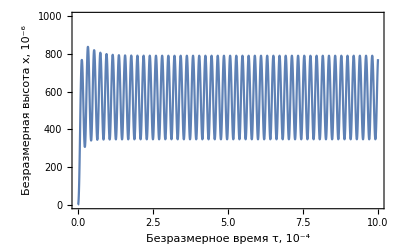

```mathematica
Plot[x[t]/.ode1,{t,0,10},ImageSize->{1000},PlotRange->{{0,10},{0,1000}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Безразмерное время τ, 10^-4",28,FontFamily->"Times New Roman"],Style["Безразмерная высота x, 10^-6",28,FontFamily->"Times New Roman"]}]
```

```mathematica
func=x/.ode1[[1]]
```

InterpolatingFunction[{{0, 1000.0000000000000000}}, <>]

```mathematica
NMaximize[{func[x],4.<x<4.2},x]
```

{790.409,{x→4.05276}}

```mathematica
max= NMaximize[{func[x],4.8<x<5.},x]
```

{790.407,{x→4.87657}}

```mathematica
NMaximize[{func[x],4.2<x<4.4},x]
```

{790.408,{x→4.25871}}

```mathematica
NMinimize[{func[x],4.<x<4.2},x]
```

{347.461,{x→4.15808}}

```mathematica
NMinimize[{func[x],4.2<x<4.4},x]
```

{347.461,{x→4.36404}}

```mathematica
min=NMinimize[{func[x],4.8<x<5.},x]
```

{347.462,{x→4.9819}}

```mathematica
amp=max[[1]]-min[[1]]
```

442.945

```mathematica
amp 10^-6 0.03//ScientificForm
```

1.32884×10^-5

```mathematica
t=2π/√(ap/3)//ScientificForm
```

2.04665×10^-5

```mathematica
disp0=(xm 3^(1/2))/ap^(3/2)//ScientificForm
```

1.98385×10^-4

```mathematica
√(ap/3)
```

306998.

```mathematica
300((x/.min[[2]])-(x/.max[[2]]))2 10^-4
```

0.00631955

```mathematica
Directory[]
```

C:\Users\Admin\Documents

```mathematica
SystemOpen["C:\\Users\\Admin\\Documents"]
```

```mathematica
ϕ0=RandomReal[{0,2π}];pts=Table[10.8Sin[(2π)/8.7 n+ϕ0]+RandomReal[{-3,3}],{n,1,20}]
```

{5.49953,2.39141,-3.68742,-12.1341,-11.8858,-6.37284,4.47108,9.14378,11.953,3.78421,1.02226,-8.65717,-7.80979,-10.4864,-4.05402,8.6916,8.25779,11.269,2.24934,-2.58419}

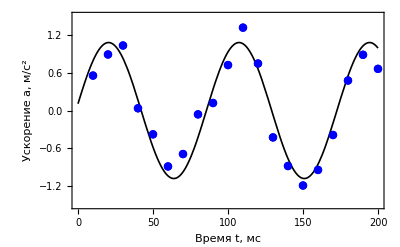

```mathematica
Show[ListPlot[points[[1;;20]],ImageSize->{1000},PlotRange->{{0,200},{-1.5,1.5}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Время t, мс",28,FontFamily->"Times New Roman"],Style["Ускорение a, м/(:0441)^2",28,FontFamily->"Times New Roman"]},PlotStyle->{Blue,PointSize[0.015]}],Plot[1.08 Sin[(2π)/8.7 0.1t+0.1],{t,0,200},PlotStyle->{Black,Thickness[0.003]}],ListPlot[points,ImageSize->{1000},PlotRange->{{0,20},{-15,15}},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->Directive[24,FontFamily->"Times New Roman"],FrameLabel->{Style["Время t, мс",28,FontFamily->"Times New Roman"],Style["Ускорение a, м/(:0441)^2",28,FontFamily->"Times New Roman"]},PlotStyle->{Blue,PointSize[0.015]}]]
```

```mathematica
2
```

```mathematica
ϕ0=RandomReal[{0,2π}];pts1=Table[10.8Sin[(2π)/8.7 n+ϕ0]+RandomReal[{-3,3}],{n,1,100}]
```

{5.55416,8.90703,10.3323,0.358035,-3.77928,-8.88249,-6.91277,-0.608411,1.19544,7.22642,13.1701,7.46837,-4.26914,-8.81403,-11.9141,-9.43709,-3.88823,4.76881,8.85361,6.62054,2.88196,-5.54699,-8.6622,-12.9199,-3.4838,0.243387,5.23735,13.2644,7.90342,1.89876,-4.4892,-8.69115,-9.95003,-2.91629,1.10991,11.5347,11.5053,7.42844,1.10885,-8.95786,-9.15333,-8.60484,-3.06476,6.43984,9.21822,9.58015,6.33204,-3.1985,-7.81751,-10.5159,-6.43055,2.04835,4.77608,10.5268,10.9696,2.27105,-5.04382,-7.20984,-7.22954,-6.75115,5.32932,8.54768,7.74907,9.22418,0.846345,-7.21898,-10.0701,-8.53883,-1.07185,4.1076,12.2239,12.0516,7.22621,-0.676368,-11.5354,-11.8492,-8.0609,-2.48384,7.06467,11.5,7.5882,5.4787,-3.10179,-10.7816,-10.4749,-2.95757,0.491253,5.84292,8.67195,10.3064,0.367603,-3.94052,-12.6824,-8.9577,-4.11906,5.57043,11.1913,12.8812,8.31136,-0.17055}

```mathematica
Export["points1.dat",%72]
```

points1.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["points1.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["points1.dat"]]]
```

```mathematica
Do[Block[{ω=RandomReal[{7.3,10.1}],amp=RandomReal[{9.1,10.8}]},Export["points"<>ToString[i]<>".dat",Table[amp Sin[(2π)/ω n+ϕ0]+RandomReal[{-3,3}],{n,1,100}]]],{i,2,10}]
```

```mathematica
Directory[]
```

C:\Users\Admin\Documents

```mathematica
SystemOpen["C:\\Users\\Admin\\Documents"]
```

```mathematica
Import["d:/downloads/points2.dat","Data"]//Flatten
```

{8.97461,8.01292,5.051,-2.48767,-5.60568,-11.8347,-4.83362,0.333251,6.24057,10.9221,7.87223,0.867124,-8.75996,-8.51184,-6.82859,-1.34931,5.78112,10.4029,10.8297,-0.243844,-5.31835,-9.33233,-6.76168,-1.95924,8.40511,10.03,12.1843,4.57957,-7.5349,-11.5245,-7.68064,-4.86624,6.30321,8.66762,7.51831,2.90657,-2.22596,-10.8131,-12.4529,-3.68331,4.47077,10.129,9.30776,6.91137,-5.21458,-6.22874,-8.93336,-4.73191,-0.956886,7.54324,12.6495,7.43839,-3.02456,-8.16723,-9.92772,-7.24924,-1.83917,9.73854,10.2228,6.04252,-0.00189705,-9.8107,-7.78398,-6.80414,1.22952,8.42256,8.95599,10.9989,2.85398,-5.30299,-7.97505,-9.08432,-4.65266,8.02174,9.88223,8.5444,0.0675322,-7.99292,-7.54954,-7.42912,-5.30686,7.15359,10.3525,7.5293,3.07693,-3.83468,-10.4315,-10.3111,-5.28546,2.47709,10.023,10.5993,4.6807,-2.43987,-7.3003,-11.7938,-8.24955,0.582582,8.83483,9.89792}

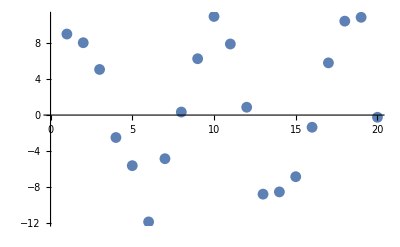

```mathematica
ListPlot[%135[[1;;20]]]
```

```mathematica
Import["d:/downloads/points3.dat","Data"]//Flatten
```

{7.80799,9.18143,8.80573,2.16561,-5.18738,-7.30815,-9.66025,-7.40341,3.14282,6.75333,10.213,8.25211,2.31913,-2.82611,-11.2833,-9.23086,-6.18184,0.17955,8.06676,7.38075,10.5363,4.0767,-3.84989,-5.12382,-9.06306,-7.13176,1.0592,7.38679,6.36826,9.46116,6.09502,-4.08061,-5.19153,-11.5452,-10.323,-0.873786,2.82259,6.96528,6.90647,3.05236,-3.51073,-8.66068,-9.23178,-7.40225,0.145416,4.14525,8.64519,11.9963,6.27072,-1.53495,-5.38533,-7.16894,-9.031,-1.06521,3.87688,11.1182,6.62179,5.01184,1.06854,-7.48574,-8.99925,-10.3521,-1.51901,4.32248,6.05976,8.78939,9.07911,2.97611,-3.8142,-11.9773,-11.9622,-5.33908,2.21534,6.34566,10.5832,8.4157,3.37278,-5.22709,-9.45976,-11.363,-5.77597,1.59055,5.28106,9.3495,6.86913,2.89861,-2.34239,-5.52076,-7.64613,-4.73796,-0.893511,7.36001,9.5034,6.90979,1.97351,-1.2956,-7.46359,-11.5801,-5.03779,1.26338}

```mathematica
(7.3+10.1)/2
```

8.7

```mathematica
(9.1+10.8)/2
```

9.95

```mathematica
omega=(2π)/0.0087
```

722.205

```mathematica
10.2/omega^2
```

0.000019556

```mathematica
%125 0.9/8.7
```

74.7109

```mathematica
%129 √(4((%128)/(%125))^2+(1.4/10.2)^2)
```

4.85544×10^-6

```mathematica
Do[Do[Block[{ω=RandomReal[{4.7,15.4}],amp=RandomReal[{3.1,8.4}]},Export["ptsothervessels"<>ToString[i]<>".dat",Table[amp Sin[(2π)/ω n+ϕ0]+RandomReal[{-3,3}],{n,1,100}]]],{i,1,8}],{i,1,5}]
```

```mathematica
√(xm/(8ag(ap+ag)))
```

0.00050884

```mathematica
%20
```

{{x→InterpolatingFunction[{{0, 1000.0000000000000000}}, <>]}}

```mathematica
func=x/.%20[[1]]
```

InterpolatingFunction[{{0, 1000.0000000000000000}}, <>]

```mathematica
func'[999]
```

2954.2434266

```mathematica
func'''[999]
```

-2.1169076×10^6

```mathematica
%41/%40
```

-716.56506

```mathematica
%42 10^8
```

-7.1656506×10^10

```mathematica
(3.07 10^5)^2
```

9.4249×10^10

```mathematica
ap %40+10^8 3%41
```

2.0022×10^14

```mathematica
ap %40
```

8.35293×10^14

```mathematica
(x''[t]+ap)x'[t]+(x[t]+xv)x'''[t]==xm-x[t] √(8xm(x''[t]+ag)(x''[t]+ap))/.x->Function[t,A+B Sin[Ω t]]//FullSimplify
```

-2. B Ω Cos[t Ω] (-1.41372×10^11+(0.5 A+0.5 xv) Ω^2+B Ω^2 Sin[t Ω])==1.72202×10^13-1.17372×10^7 (A+B Sin[t Ω]) √((-2.82743×10^11+B Ω^2 Sin[t Ω]) (-2.94×10^7+B Ω^2 Sin[t Ω]))

```mathematica
-2. B Ω Cos[t Ω] (-1.4137166941154068*^11+0.5 xv Ω^2)==1.7220166666666668*^13-1.1737177400607582*^7 (A+B Sin[t Ω]) √((-2.8274333882308136*^11) (-2.9400000000000004*^7))
```

-2. B Ω (-1.41372×10^11+0.5 xv Ω^2) Cos[t Ω]==1.72202×10^13-3.38402×10^16 (A+B Sin[t Ω])

```mathematica
pts=Import["points1.dat"];
```

```mathematica
points=Table[{10i,pts[[i,1]]},{i,1,Length[pts]}];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["points10.dat"]]]
```

```mathematica
z={5,4}
```

{5,4}

```mathematica
d=z/10
```

{1/2,2/5}

```mathematica
points
```

{{10,0.555416},{20,0.890703},{30,1.03323},{40,0.0358035},{50,-0.377928},{60,-0.888249},{70,-0.691277},{80,-0.0608411},{90,0.119544},{100,0.722642},{110,1.31701},{120,0.746837},{130,-0.426914},{140,-0.881403},{150,-1.19141},{160,-0.943709},{170,-0.388823},{180,0.476881},{190,0.885361},{200,0.662054},{210,0.288196},{220,-0.554699},{230,-0.86622},{240,-1.29199},{250,-0.34838},{260,0.0243387},{270,0.523735},{280,1.32644},{290,0.790342},{300,0.189876},{310,-0.44892},{320,-0.869115},{330,-0.995003},{340,-0.291629},{350,0.110991},{360,1.15347},{370,1.15053},{380,0.742844},{390,0.110885},{400,-0.895786},{410,-0.915333},{420,-0.860484},{430,-0.306476},{440,0.643984},{450,0.921822},{460,0.958015},{470,0.633204},{480,-0.31985},{490,-0.781751},{500,-1.05159},{510,-0.643055},{520,0.204835},{530,0.477608},{540,1.05268},{550,1.09696},{560,0.227105},{570,-0.504382},{580,-0.720984},{590,-0.722954},{600,-0.675115},{610,0.532932},{620,0.854768},{630,0.774907},{640,0.922418},{650,0.0846345},{660,-0.721898},{670,-1.00701},{680,-0.853883},{690,-0.107185},{700,0.41076},{710,1.22239},{720,1.20516},{730,0.722621},{740,-0.0676368},{750,-1.15354},{760,-1.18492},{770,-0.80609},{780,-0.248384},{790,0.706467},{800,1.15},{810,0.75882},{820,0.54787},{830,-0.310179},{840,-1.07816},{850,-1.04749},{860,-0.295757},{870,0.0491253},{880,0.584292},{890,0.867195},{900,1.03064},{910,0.0367603},{920,-0.394052},{930,-1.26824},{940,-0.89577},{950,-0.411906},{960,0.557043},{970,1.11913},{980,1.28812},{990,0.831136},{1000,-0.017055}}